```mathematica
sig1=Table[Cos[2 π *0.3* k] +Cos[2 π *0.1* k] ,{k,1,1500}];
sig2=Table[0.8*(Cos[2 π *0.3* k+2π*0.15] +Cos[2 π *0.1* k+2π*0.25]),{k,1,1500}];
sig3=Table[0.95*(Cos[2 π *0.3* k+2π*0.3] +Cos[2 π *0.1* k+2π*0.5]),{k,1,1500}];
sig4=Table[0.85*(Cos[2 π *0.3* k+2π*0.45] +Cos[2 π *0.1* k+2π*0.75]),{k,1,1500}];
```

```mathematica
SigM = Transpose[{{sig1},{sig2},{sig3},{sig4}}];
```

```mathematica
SVDFunc[x_,a_?NumberQ]:=ListPlot[Transpose[SingularValueDecomposition[x][[1;3]]][[a]],Joined->True, PlotRange->All]
```

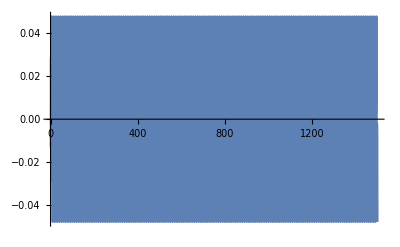

```mathematica
SVDFunc[SigM,1]
```

```mathematica
SVDVector[x_,a_?NumberQ]:=Transpose[SingularValueDecomposition[x][[1;3]]][[a]];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;NumPlace[x]+4]],AbsFourier[x][[1;;NumPlace[x]+4]]}],PlotRange->All]
```

```mathematica
SVDVector1 = SVDVector[SigM,1];
```

```mathematica
Freq[SVDVector1]
```

0.3

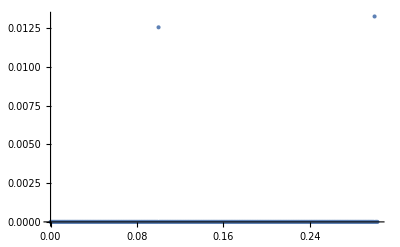

```mathematica
TruePlot[SVDVector1]
```

0.1

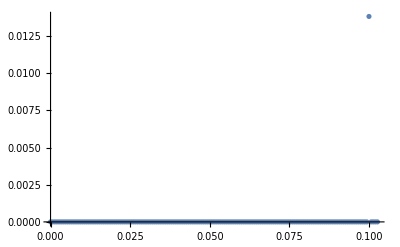

```mathematica
SVDVector2 = SVDVector[SigM,2];
Freq[SVDVector2]
TruePlot[SVDVector2]
```